## Rossler System

```mathematica
Clear[a,b,c]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z, x +a y,b+z (x  - c)}
Df[{a_,b_,c_}][{x_,y_,z_}]=D[f[{a,b,c}][{x,y,z}],{{x,y,z}}];
MatrixForm[Df[{a,b,c}][{x,y,z}]]
```

(0 | -1 | -1
1 | a | 0
z | 0 | -c+x)

Numerical solution with standard parameters.

```mathematica
y0=10RandomReal[{-1,1},3];

TMax=123;
{a,b,c}={0.2,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

### Basic Plots

```mathematica
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^3]
```

-Graphics3D-

### Sensitivity Plot

```mathematica
TabView[{
"plain"->Plot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All],
"log"->LogPlot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All]
}]
```

12

### Changing the Parameters

Numerical solution with different parameters. Looks like it joins back up again!

```mathematica
y0=10RandomReal[{-1,1},3];
TMax=180;
{a,b,c}={0.1,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[{a,b,c}][y[t]],y[0]==y0,
J'[t]==Df[{a,b,c}][y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

Looks as though there is an attractive periodic solution that winds round three times before it repeats.

```mathematica
TabView[{
"3D"->ParametricPlot3D[ySol[t],{t,0.8TMax, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}],
"3 fun"->Plot[ySol[t],{t,0.8 TMax, TMax},
AxesLabel->{"t"," "}],
"y_3"->LogPlot[ySol[t]⟦3⟧,{t,0.8 TMax, TMax},
AxesLabel->{"t","y_3"},PlotRange->All],
"log ||y(T)-y(t)(||)^2"->LogPlot[
Norm[ySol[t]-ySol[TMax]]^2,{t,0.8 TMax, TMax},
AxesLabel->{"t"," "},
PlotRange->All]
}]
```

1234

Since y'=f[y] the derivative of g[t]=(y[t]-y[TMax]).(y[t]-y[TMax]) is  		
	g'[t]=2(y[t]-y[TMax]).y'[t]=2(y[t]-y[TMax]).f[y[t]]
which of course we can plot

```mathematica
Clear[g,dg,t]
g[t_?NumericQ]:=(ySol[t]-ySol[TMax]).(ySol[t]-ySol[TMax])
dg[t_?NumericQ]:=2(ySol[t]-ySol[TMax]).f[{a,b,c}][ySol[t]]
```

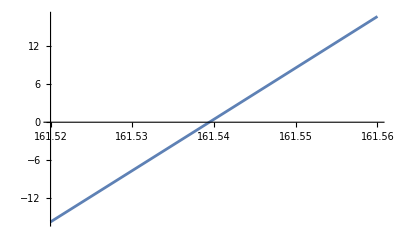

```mathematica
Plot[g'[t],{t, 161.52,161.56},
PlotRange->All]
```

```mathematica
tMin=t/.FindRoot[g'[t]==0,{t,161.5}]
g[tMin]
ParametricPlot3D[ySol[t],{t,tMin+0.05, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}]
```

161.539

1.11186×10^-9

-Graphics3D-

```mathematica
{t->161.53942721802423}
```

```mathematica
2
```

170.612

{60.026,{t→167.465}}

InterpolatingFunction::dmval: Input value {204.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

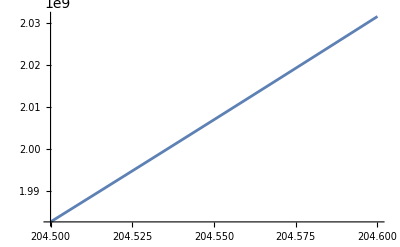

```mathematica
tMin=t/.FindRoot[dg[t]==0,{t, 170}]
FindMinimum[g[t],{t, 170}]
LogPlot[g[t],{t, 0.8 TMax, TMax}];
Plot[g[t],{t, 204.5, 204.6},PlotRange->All,PlotPoints->10^3]
```

204.008

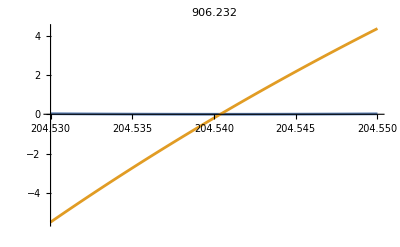

```mathematica
Plot[{g[t],dg[t]},{t, 204.53,204.55},
Prolog->{Red,PointSize[0.02],Point[{tMin,g[tMin]}]},
PlotLabel->g[tMin]
]
```

```mathematica
?FindRoot
```

```mathematica
g[204.809]
```

9.60444

```mathematica
?FindMinimum
```

```mathematica
g[0.1]
```

199.095

```mathematica
Evaluate[dg[t]]
```

2 {-9.74649-InterpolatingFunction[{{0., 223.}}, <>][t],-5.0321-InterpolatingFunction[{{0., 223.}}, <>][t],0.00835523-InterpolatingFunction[{{0., 223.}}, <>][t]}.(-InterpolatingFunction[{{0., 223.}}, <>][t])

```mathematica
?FindRoot
```

```mathematica
dg[0.1]
```

-292.801